```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[8],Join[Table[{i,i-1},{i,Range[2,8,1]}],Table[{i,i+1},{i,Range[1,8,1]}]]->-t]
```

```mathematica
T[t_]:=T[t]=t*IdentityMatrix[8]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,1,0]],A:=Inverse[β[ω,δ,1,0]],T:=T[1]},Do[J=Inverse[IdentityMatrix[8]-A.T.J.T].A,60000];J=J]
```

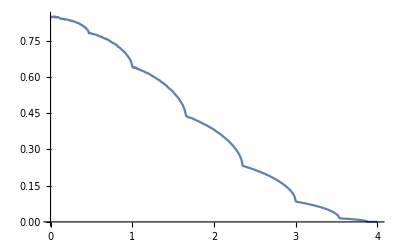

```mathematica
ListLinePlot[Table[{ω,-Im[LEFT[ω,0.0001,1,0]][[1,1]]},{ω,Range[0,4,0.01]}]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[8]-g[ω,δ,t,ϵ].T[1].LEFT[ω,δ,t,ϵ].T[1]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[8]-g[ω,δ,t,ϵ].T[1].LEFT[ω,δ,t,ϵ].T[1]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[8]-SL[ω,δ,1,0].T[1].SR[ω,δ,1,0].T[1]].SL[ω,δ,1,0]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[8]-SR[ω,δ,1,0].T[1].SL[ω,δ,1,0].T[1]].SR[ω,δ,1,0]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,1,0].T[1].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T[1].grr[ω,δ,t,ϵ].T[1]-T[1].GNON[ω,δ,t,ϵ].T[1].GNON[ω,δ,t,ϵ]]
```

```mathematica
pris=Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[0,4,0.01]}]
```

{{0.,7.99996},{0.01,7.99996},{0.02,7.99998},{0.03,7.99998},{0.04,7.99998},{0.05,7.99997},{0.06,7.99996},{0.07,7.99997},{0.08,7.99999},{0.09,7.99996},{0.1,7.99996},{0.11,7.99994},{0.12,7.9935},{0.13,7.},{0.14,6.99999},{0.15,6.99999},{0.16,6.99998},{0.17,6.99998},{0.18,6.99997},{0.19,6.99998},{0.2,6.99997},{0.21,6.99998},{0.22,6.99996},{0.23,6.99999},{0.24,6.99998},{0.25,6.99997},{0.26,6.99997},{0.27,6.99998},{0.28,6.99999},{0.29,6.99998},{0.3,6.99999},{0.31,6.99998},{0.32,6.99998},{0.33,6.99997},{0.34,6.99998},{0.35,6.99998},{0.36,6.99999},{0.37,6.99997},{0.38,6.99997},{0.39,6.99998},{0.4,6.99997},{0.41,6.99996},{0.42,6.99996},{0.43,6.99997},{0.44,6.99997},{0.45,6.99997},{0.46,6.99994},{0.47,6.00053},{0.48,5.99999},{0.49,5.99998},{0.5,5.99998},{0.51,5.99995},{0.52,5.99998},{0.53,5.99999},{0.54,5.99997},{0.55,5.99996},{0.56,5.99996},{0.57,5.99999},{0.58,5.99997},{0.59,5.99997},{0.6,5.99999},{0.61,5.99996},{0.62,5.99997},{0.63,5.99998},{0.64,5.99999},{0.65,5.99998},{0.66,5.99997},{0.67,5.99999},{0.68,5.99996},{0.69,5.99996},{0.7,5.99998},{0.71,5.99997},{0.72,5.99999},{0.73,5.99998},{0.74,5.99997},{0.75,5.99998},{0.76,5.99997},{0.77,5.99998},{0.78,5.99999},{0.79,5.99997},{0.8,5.99996},{0.81,5.99997},{0.82,5.99999},{0.83,5.99997},{0.84,5.99997},{0.85,5.99999},{0.86,5.99996},{0.87,5.99999},{0.88,5.99999},{0.89,5.99996},{0.9,5.99998},{0.91,5.99998},{0.92,5.99998},{0.93,5.99997},{0.94,5.99996},{0.95,5.99995},{0.96,5.99997},{0.97,5.99995},{0.98,5.99996},{0.99,5.99993},{1.,5.49995},{1.01,4.99998},{1.02,4.99996},{1.03,4.99996},{1.04,4.99995},{1.05,4.99995},{1.06,4.99997},{1.07,4.99996},{1.08,4.99997},{1.09,4.99998},{1.1,4.99997},{1.11,4.99996},{1.12,4.99998},{1.13,4.99998},{1.14,4.99997},{1.15,4.99998},{1.16,4.99997},{1.17,4.99995},{1.18,4.99997},{1.19,4.99997},{1.2,4.99997},{1.21,4.99999},{1.22,4.99997},{1.23,4.99997},{1.24,4.99995},{1.25,4.99998},{1.26,4.99995},{1.27,4.99996},{1.28,5.},{1.29,4.99998},{1.3,4.99998},{1.31,4.99999},{1.32,4.99998},{1.33,4.99998},{1.34,4.99998},{1.35,4.99998},{1.36,4.99996},{1.37,4.99997},{1.38,4.99996},{1.39,4.99995},{1.4,4.99997},{1.41,4.99998},{1.42,4.99994},{1.43,4.99997},{1.44,4.99996},{1.45,4.99997},{1.46,4.99995},{1.47,4.99997},{1.48,4.99996},{1.49,4.99995},{1.5,4.99995},{1.51,4.99996},{1.52,4.99996},{1.53,4.99996},{1.54,4.99997},{1.55,4.99995},{1.56,4.99997},{1.57,4.99995},{1.58,4.99996},{1.59,4.99997},{1.6,4.99998},{1.61,4.99998},{1.62,4.99996},{1.63,4.99997},{1.64,4.99994},{1.65,4.99963},{1.66,4.00004},{1.67,3.99998},{1.68,3.99999},{1.69,3.99997},{1.7,3.99997},{1.71,3.99997},{1.72,3.99999},{1.73,3.99996},{1.74,3.99997},{1.75,3.99997},{1.76,3.99999},{1.77,3.99998},{1.78,3.99996},{1.79,3.99998},{1.8,3.99999},{1.81,3.99998},{1.82,3.99997},{1.83,3.99997},{1.84,3.99998},{1.85,3.99997},{1.86,3.99997},{1.87,3.99996},{1.88,3.99997},{1.89,3.99997},{1.9,3.99997},{1.91,3.99998},{1.92,3.99996},{1.93,3.99996},{1.94,3.99996},{1.95,3.99996},{1.96,3.99998},{1.97,3.99998},{1.98,3.99998},{1.99,3.99997},{2.,3.99997},{2.01,3.99998},{2.02,3.99997},{2.03,3.99998},{2.04,3.99996},{2.05,3.99998},{2.06,3.99999},{2.07,3.99997},{2.08,3.99997},{2.09,3.99996},{2.1,3.99997},{2.11,4.},{2.12,3.99997},{2.13,3.99997},{2.14,3.99998},{2.15,3.99999},{2.16,3.99998},{2.17,3.99999},{2.18,3.99999},{2.19,3.99998},{2.2,3.99998},{2.21,3.99999},{2.22,4.},{2.23,3.99999},{2.24,3.99999},{2.25,3.99999},{2.26,3.99998},{2.27,3.99998},{2.28,4.},{2.29,3.99999},{2.3,3.99998},{2.31,3.99999},{2.32,3.99997},{2.33,3.99997},{2.34,3.99994},{2.35,3.00034},{2.36,3.},{2.37,2.99998},{2.38,2.99999},{2.39,2.99999},{2.4,2.99999},{2.41,2.99999},{2.42,3.},{2.43,2.99998},{2.44,2.99999},{2.45,2.99998},{2.46,3.},{2.47,2.99998},{2.48,2.99999},{2.49,2.99999},{2.5,2.99999},{2.51,3.},{2.52,2.99999},{2.53,3.},{2.54,2.99999},{2.55,2.99999},{2.56,2.99999},{2.57,3.},{2.58,2.99999},{2.59,3.},{2.6,2.99999},{2.61,2.99999},{2.62,3.},{2.63,2.99999},{2.64,3.},{2.65,2.99999},{2.66,3.},{2.67,2.99999},{2.68,2.99999},{2.69,2.99999},{2.7,2.99999},{2.71,2.99999},{2.72,2.99999},{2.73,3.},{2.74,2.99999},{2.75,2.99999},{2.76,3.},{2.77,3.},{2.78,2.99999},{2.79,3.},{2.8,2.99999},{2.81,3.},{2.82,3.},{2.83,3.},{2.84,3.},{2.85,3.},{2.86,3.},{2.87,3.},{2.88,3.},{2.89,3.},{2.9,3.},{2.91,3.},{2.92,3.},{2.93,3.},{2.94,3.},{2.95,3.},{2.96,3.},{2.97,3.},{2.98,2.99999},{2.99,2.99997},{3.,2.49999},{3.01,2.00002},{3.02,2.},{3.03,2.},{3.04,2.},{3.05,2.},{3.06,2.},{3.07,2.},{3.08,2.},{3.09,2.},{3.1,2.},{3.11,2.},{3.12,2.},{3.13,2.},{3.14,2.},{3.15,2.},{3.16,2.},{3.17,2.},{3.18,2.},{3.19,2.},{3.2,2.},{3.21,2.},{3.22,2.},{3.23,2.},{3.24,2.},{3.25,2.},{3.26,2.},{3.27,2.},{3.28,2.},{3.29,2.},{3.3,2.},{3.31,2.},{3.32,2.},{3.33,2.},{3.34,2.},{3.35,2.},{3.36,2.},{3.37,2.},{3.38,2.},{3.39,2.},{3.4,2.},{3.41,2.},{3.42,2.},{3.43,2.},{3.44,2.},{3.45,2.},{3.46,2.},{3.47,2.},{3.48,2.},{3.49,2.},{3.5,2.},{3.51,1.99999},{3.52,1.99998},{3.53,1.99943},{3.54,1.00004},{3.55,1.00001},{3.56,1.},{3.57,1.},{3.58,1.},{3.59,1.},{3.6,1.},{3.61,1.},{3.62,1.},{3.63,1.},{3.64,1.},{3.65,1.},{3.66,1.},{3.67,1.},{3.68,1.},{3.69,1.},{3.7,1.},{3.71,1.},{3.72,1.},{3.73,1.},{3.74,1.},{3.75,1.},{3.76,1.},{3.77,1.},{3.78,1.},{3.79,1.},{3.8,1.},{3.81,0.999999},{3.82,0.999999},{3.83,0.999999},{3.84,0.999998},{3.85,0.999997},{3.86,0.999993},{3.87,0.999972},{3.88,0.00648459},{3.89,0.0000220888},{3.9,5.84101×10^-6},{3.91,2.64451×10^-6},{3.92,1.50192×10^-6},{3.93,9.67492×10^-7},{3.94,6.75391×10^-7},{3.95,4.98544×10^-7},{3.96,3.8342×10^-7},{3.97,3.04303×10^-7},{3.98,2.47592×10^-7},{3.99,2.05551×10^-7},{4.,1.73514×10^-7}}

```mathematica
Clear[imp,imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8]
```

```mathematica
misfit[ϵ1_,y_,x_]:=Module[{Tin=T[1],μ1=RandomInteger[{1,8}], μ2=RandomInteger[{1,8}], μ3=RandomInteger[{1,8}], μ4=RandomInteger[{1,8}],μ5=RandomInteger[{1,8}], μ6=RandomInteger[{1,8}], μ7=RandomInteger[{1,8}],μ8=RandomInteger[{1,8}], μ9=RandomInteger[{1,8}], μ10=RandomInteger[{1,8}], μ11=RandomInteger[{1,8}],μ12=RandomInteger[{1,8}], μ13=RandomInteger[{1,8}], μ14=RandomInteger[{1,8}]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-0]]];tra:= Module[{},list={RandomSample[{imp7,imp10,imp9,imp,imp1,imp,imp,imp,imp9,imp9,imp5,imp,imp8,imp11,imp13,imp,imp3,imp3,imp,imp,imp14,imp,imp13,imp8,imp,imp11,imp,imp8,imp7,imp,imp,imp,imp5,imp,imp,imp14,imp,imp5,imp10,imp,imp10,imp2,imp6,imp,imp2,imp11,imp,imp6,imp4,imp,imp,imp,imp,imp6,imp,imp,imp,imp4,imp1,imp,imp10,imp,imp2,imp13,imp,imp4,imp14,imp7,imp,imp11,imp8,imp4,imp7,imp,imp12,imp,imp,imp12,imp14,imp,imp,imp3,imp5,imp,imp1,imp,imp,imp12,imp13,imp2,imp1,imp,imp6,imp12,imp,imp3,imp9,imp,imp,imp}]};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[8]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[8]-sl1.Tin.SR[ω,0.0001,1,0].Tin].sl1;
Ir1:=Inverse[IdentityMatrix[8]-SR[ω,0.0001,1,0].Tin.sl1.Tin].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].Tin.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]>10,10,Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]]];
b];
m5=Table[{ω,tra},{ω,Range[0,4,0.01]}];
A1:=Module[{B1=Transpose[{m5[[1;;399]][[;;,1]],Abs[(m5[[1;;399,2]]-Import["/home/shardulmukim/PhD/fwi/8imp3.dat"][[1;;399,;;]][[;;,2]])]}]},Integrate[Interpolation[B1][ω],{ω,y,x}]];
A2:=Module[{B1=Transpose[{m5[[1;;399]][[;;,1]],Abs[(m5[[1;;399,2]]-Import["/home/shardulmukim/PhD/fwi/8imp4.dat"][[1;;399,;;]][[;;,2]])]}]},Integrate[Interpolation[B1][ω],{ω,y,x}]];
A3:=Module[{B1=Transpose[{m5[[1;;399]][[;;,1]],Abs[(m5[[1;;399,2]]-Import["/home/shardulmukim/PhD/fwi/8imp5.dat"][[1;;399,;;]][[;;,2]])]}]},Integrate[Interpolation[B1][ω],{ω,y,x}]];
A4:=Module[{B1=Transpose[{m5[[1;;399]][[;;,1]],Abs[(m5[[1;;399,2]]-Import["/home/shardulmukim/PhD/fwi/8imp6.dat"][[1;;399,;;]][[;;,2]])]}]},Integrate[Interpolation[B1][ω],{ω,y,x}]];
A5:=Module[{B1=Transpose[{m5[[1;;399]][[;;,1]],Abs[(m5[[1;;399,2]]-Import["/home/shardulmukim/PhD/fwi/8imp7.dat"][[1;;399,;;]][[;;,2]])]}]},Integrate[Interpolation[B1][ω],{ω,y,x}]];
A6:=Module[{B1=Transpose[{m5[[1;;399]][[;;,1]],Abs[(m5[[1;;399,2]]-Import["/home/shardulmukim/PhD/fwi/8imp8.dat"][[1;;399,;;]][[;;,2]])]}]},Integrate[Interpolation[B1][ω],{ω,y,x}]];
A7:=Module[{B1=Transpose[{m5[[1;;399]][[;;,1]],Abs[(m5[[1;;399,2]]-Import["/home/shardulmukim/PhD/fwi/8imp9.dat"][[1;;399,;;]][[;;,2]])]}]},Integrate[Interpolation[B1][ω],{ω,y,x}]];
{A1,A2,A3,A4,A5,A6,A7}
]
```

```mathematica
f[x_]:=f[x]=Table[misfit[0.6,0,x],100]
```

```mathematica
h[x_]:=h[x]=Table[misfit[0.5,0,x],20]
```

```mathematica
Table[h[x],{x,Range[0.1,3.8,0.3]}]
```

{{{0.188415,0.0940767,0.0714677,0.091434,0.128746,0.18277,0.230189},{0.174,0.0931171,0.0871951,0.08873,0.11379,0.175364,0.226873},{0.223151,0.119588,0.106368,0.132072,0.168998,0.217506,0.264925},{0.160493,0.0645197,0.0538802,0.0821725,0.123395,0.185161,0.237048},{0.163311,0.0791933,0.091932,0.112792,0.138023,0.188378,0.239887},{0.169413,0.0888322,0.0782491,0.0755385,0.0969776,0.15635,0.208237},{0.167469,0.094437,0.0882537,0.0876754,0.118219,0.179793,0.231302},{0.16761,0.0668582,0.042901,0.0591338,0.106258,0.164474,0.215983},{0.169988,0.101563,0.0817061,0.0859596,0.121464,0.167217,0.209298},{0.209993,0.103611,0.0924633,0.125986,0.174882,0.236802,0.288689},{0.237365,0.18061,0.159443,0.15364,0.162664,0.193764,0.233752},{0.173794,0.113416,0.0976027,0.103239,0.122699,0.156702,0.201315},{0.189004,0.0889335,0.0514752,0.075096,0.122677,0.177594,0.225013},{0.24157,0.136165,0.121252,0.147113,0.183164,0.232561,0.279601},{0.159619,0.0624748,0.0695721,0.083507,0.124508,0.186429,0.238316},{0.134346,0.0406108,0.0558526,0.0711102,0.101469,0.160745,0.212633},{0.210081,0.127527,0.100075,0.10011,0.121333,0.162965,0.210006},{0.159782,0.0884802,0.0791574,0.0955595,0.127456,0.167232,0.216489},{0.211562,0.138493,0.131601,0.130072,0.151771,0.182465,0.214966},{0.168404,0.0828889,0.0640423,0.069832,0.112941,0.174515,0.226024}},{{0.881873,0.499521,0.409039,0.532901,0.662067,0.747293,0.762358},{0.905641,0.495258,0.373384,0.496815,0.648474,0.734515,0.75767},{1.12377,0.717783,0.477301,0.547818,0.665924,0.736156,0.760342},{0.809154,0.389415,0.34768,0.526645,0.660428,0.749291,0.783839},{0.834724,0.433221,0.36289,0.534054,0.721922,0.839222,0.871443},{0.921718,0.537153,0.361405,0.445663,0.613044,0.706491,0.7396},{0.920014,0.532059,0.383115,0.528434,0.666271,0.754971,0.768814},{1.04311,0.660771,0.488977,0.524833,0.626223,0.689589,0.701718},{1.05906,0.707276,0.457012,0.440768,0.526121,0.587598,0.610821},{0.999103,0.66461,0.474916,0.577474,0.713422,0.774417,0.759772},{0.917445,0.557174,0.348132,0.450386,0.573417,0.622042,0.627262},{1.0169,0.700153,0.473024,0.450599,0.532142,0.617268,0.6491},{0.888374,0.461603,0.344599,0.49025,0.64106,0.734474,0.756272},{0.86743,0.516204,0.470107,0.614709,0.743133,0.822096,0.849143},{0.951757,0.573709,0.368924,0.42224,0.541048,0.624591,0.646635},{0.770532,0.426486,0.412114,0.610659,0.756258,0.813896,0.804106},{0.916112,0.525694,0.420609,0.570763,0.727252,0.827808,0.841129},{0.860989,0.462612,0.371783,0.534368,0.696679,0.796779,0.812362},{0.958984,0.55016,0.404766,0.507525,0.658754,0.735291,0.775761},{1.01111,0.571906,0.368561,0.508065,0.668995,0.751848,0.765847}},{{1.56813,0.961363,0.669118,0.825511,1.08466,1.27662,1.38741},{1.62032,1.01464,0.666314,0.817503,1.0525,1.24813,1.3364},{1.42921,0.820752,0.602308,0.890517,1.16937,1.35332,1.46877},{1.63241,1.04651,0.740473,0.896971,1.12309,1.28965,1.37128},{1.40828,0.852669,0.612946,0.879655,1.17179,1.345,1.44277},{1.45334,0.803937,0.649084,0.96849,1.25806,1.44534,1.54549},{1.56032,0.941152,0.703301,0.95175,1.25637,1.4512,1.55366},{1.51027,0.963181,0.726149,0.909175,1.18639,1.36873,1.46837},{1.45855,0.92355,0.733792,0.936762,1.18702,1.38021,1.48379},{1.41869,0.823134,0.654327,0.906352,1.18391,1.38807,1.49211},{1.38445,0.841927,0.758792,1.11364,1.39805,1.57865,1.65838},{1.59225,0.91274,0.60433,0.756659,1.02632,1.23005,1.33602},{1.47281,1.04402,0.880097,1.0605,1.30045,1.43291,1.48201},{1.32969,0.697292,0.504302,0.830644,1.13847,1.33971,1.43741},{1.60688,1.04112,0.795178,0.983974,1.22498,1.39197,1.45541},{1.36155,0.861262,0.694266,0.930946,1.17513,1.32832,1.38758},{1.40347,0.833418,0.702481,0.959711,1.24257,1.41079,1.48241},{1.52143,0.899696,0.669864,0.913096,1.21825,1.41826,1.51006},{1.53806,0.908785,0.664123,0.897278,1.19732,1.41179,1.52182},{1.56465,0.936889,0.718745,0.918386,1.1771,1.32491,1.39298}},{{2.08961,1.26101,0.897122,1.21751,1.62744,1.9399,2.11049},{1.92553,1.08708,0.813759,1.16586,1.59356,1.92123,2.11963},{2.07004,1.211,0.864553,1.1087,1.47058,1.74206,1.92978},{2.04517,1.27371,0.945741,1.29889,1.69896,2.00564,2.18093},{1.73656,1.00335,0.947351,1.34224,1.76534,2.03552,2.1665},{1.87566,1.12973,0.81186,1.15173,1.60139,1.9168,2.09232},{2.02862,1.18084,0.768089,1.07544,1.50976,1.82396,2.00337},{2.12241,1.24195,0.778555,1.05935,1.49443,1.80541,1.9804},{2.02572,1.17137,0.770941,1.04337,1.45939,1.80613,2.02991},{1.86671,1.13688,0.991381,1.28354,1.68862,1.98675,2.14751},{2.02368,1.17745,0.766881,1.02439,1.43245,1.74782,1.9307},{1.90698,1.06395,0.682738,1.09164,1.59772,1.95794,2.16007},{1.90097,1.07625,0.83747,1.27667,1.73536,2.06928,2.27073},{1.98734,1.16905,0.802426,1.11555,1.54322,1.86116,2.04878},{1.90603,1.04828,0.705309,1.05189,1.50198,1.81791,2.00643},{2.24289,1.32207,0.881573,1.1196,1.52365,1.84693,2.02902},{2.124,1.30664,0.845582,1.03691,1.44432,1.76825,1.96819},{2.33864,1.43124,0.90662,1.111,1.4696,1.75614,1.95851},{1.7211,0.936648,0.759518,1.16934,1.60557,1.92983,2.12645},{2.0907,1.2834,0.87123,1.17411,1.59906,1.93293,2.15578}},{{2.57678,1.58135,1.0557,1.3943,1.90377,2.36084,2.62718},{2.42946,1.47058,0.871555,1.1661,1.68304,2.10058,2.357},{2.45208,1.46094,0.932802,1.24384,1.80765,2.27721,2.58199},{2.0835,1.14718,0.909944,1.47293,2.0563,2.51523,2.79525},{2.39511,1.36726,0.811451,1.24178,1.83932,2.28926,2.56147},{2.38581,1.39767,0.973752,1.37612,1.93372,2.36151,2.65349},{2.3379,1.36333,0.947697,1.31724,1.93525,2.42627,2.74328},{2.36229,1.30244,0.890417,1.32165,1.86014,2.30625,2.59479},{2.26595,1.36527,0.918601,1.29108,1.85159,2.27813,2.54066},{2.49189,1.56728,1.21474,1.59792,2.12101,2.53907,2.80397},{2.22253,1.19644,0.871294,1.33208,1.88464,2.27044,2.53379},{2.52561,1.576,1.05486,1.42903,2.00719,2.46355,2.73645},{2.36699,1.42454,1.00733,1.44485,2.01999,2.45519,2.74628},{2.40241,1.41034,0.952555,1.3379,1.92396,2.35839,2.63877},{2.52185,1.53241,0.975954,1.32379,1.85352,2.25271,2.5123},{2.39246,1.41841,0.94337,1.27718,1.79372,2.22797,2.53681},{2.33299,1.41307,1.02604,1.49866,2.06758,2.45785,2.70451},{2.31007,1.40612,0.942894,1.34481,1.93397,2.36238,2.61071},{2.28505,1.38516,1.02971,1.47356,1.96686,2.37991,2.63906},{2.49019,1.54655,1.01777,1.3048,1.82415,2.23453,2.49867}},{{2.76802,1.55155,1.09038,1.59332,2.28157,2.83658,3.18727},{2.83647,1.80507,1.26463,1.67429,2.33559,2.87382,3.26898},{2.62148,1.48333,0.989056,1.57916,2.32155,2.92837,3.32506},{2.49701,1.34156,0.996464,1.69135,2.4456,3.01756,3.39498},{2.72297,1.65058,1.24859,1.75693,2.44764,2.99092,3.37415},{2.83655,1.63614,1.0226,1.4675,2.19655,2.78291,3.18903},{2.8951,1.75176,1.16747,1.68552,2.40679,2.97356,3.37244},{2.7569,1.63888,1.15237,1.68452,2.37765,2.93615,3.30486},{2.66611,1.44622,1.08227,1.64575,2.39717,2.98228,3.37684},{2.71671,1.58974,1.07088,1.57101,2.25956,2.82765,3.22081},{2.89633,1.72437,1.08635,1.46098,2.1833,2.78204,3.17754},{2.71991,1.60041,1.14568,1.65019,2.33652,2.86574,3.23853},{2.73399,1.70348,1.19397,1.63906,2.32555,2.88567,3.26228},{2.76457,1.61304,1.08286,1.56191,2.23106,2.77756,3.15113},{2.82993,1.68978,1.10268,1.55242,2.27673,2.8612,3.26562},{2.7466,1.62837,1.16645,1.6582,2.35004,2.87477,3.23146},{2.57861,1.47992,1.09561,1.63434,2.37985,2.96339,3.38918},{2.3855,1.3232,1.06604,1.72414,2.45032,2.98329,3.34841},{2.64541,1.56156,1.18051,1.66032,2.38694,2.96766,3.3686},{2.87312,1.70152,1.04649,1.50822,2.166,2.67133,3.01269}},{{3.30104,2.02847,1.40725,1.92865,2.72511,3.39647,3.86212},{3.13317,1.88958,1.27803,1.76432,2.5615,3.20254,3.64017},{3.28588,2.0436,1.2558,1.59734,2.34773,2.97378,3.41648},{3.07778,1.82475,1.25612,1.81227,2.63384,3.26567,3.71098},{3.13608,1.88441,1.33628,1.90286,2.67848,3.29393,3.72158},{3.14392,1.91107,1.30486,1.83914,2.63509,3.27697,3.7335},{3.05882,1.81868,1.12045,1.62052,2.39233,3.04041,3.48048},{2.94067,1.71879,1.24001,1.79532,2.57943,3.22482,3.67836},{3.2949,2.04431,1.32494,1.77284,2.54638,3.20729,3.66721},{3.24458,2.02642,1.45285,1.95129,2.71274,3.35459,3.80724},{2.97296,1.76526,1.15367,1.61032,2.38443,3.02284,3.47528},{3.15363,1.90953,1.27312,1.69528,2.48453,3.14948,3.61751},{3.15005,1.93628,1.24516,1.58178,2.36039,3.02096,3.47592},{3.06766,1.79238,1.15333,1.69451,2.52925,3.20085,3.70101},{3.22764,1.99728,1.39332,1.90731,2.67213,3.29341,3.72868},{3.05366,1.76696,1.35363,1.99811,2.81495,3.48475,3.92954},{3.1898,2.01391,1.30112,1.80305,2.58835,3.2426,3.68046},{3.05486,1.82858,1.10722,1.62942,2.40172,3.04956,3.4935},{3.2553,1.96512,1.3157,1.81224,2.58838,3.23755,3.69203},{3.01835,1.78209,1.29927,1.84622,2.66234,3.3067,3.78237}},{{3.30959,1.98298,1.31957,1.8462,2.71719,3.46082,4.0062},{3.28091,2.0284,1.45534,2.00521,2.90879,3.65579,4.21181},{3.31956,1.94066,1.33336,1.92146,2.81815,3.57182,4.13675},{3.31552,2.01806,1.42217,2.02288,2.96116,3.71931,4.2706},{3.13907,1.78828,1.25878,1.94237,2.83718,3.55945,4.09661},{2.93136,1.61909,1.22594,2.06429,2.97733,3.71341,4.25807},{3.46298,2.03719,1.33745,1.89701,2.81125,3.58044,4.14913},{3.18618,1.80268,1.20771,1.90039,2.8512,3.62716,4.18393},{3.45661,2.13016,1.44984,1.94299,2.81,3.55056,4.1047},{3.49477,2.18028,1.42616,1.88677,2.7329,3.48259,4.04682},{3.26472,1.99423,1.28007,1.81666,2.74992,3.52709,4.06847},{3.05869,1.81683,1.22448,1.89505,2.76309,3.47333,4.00195},{3.35825,1.95201,1.32868,1.90915,2.7734,3.52787,4.10734},{3.43133,2.17207,1.48396,1.97304,2.82901,3.52997,4.02469},{3.16125,1.81613,1.21118,1.87743,2.79449,3.56122,4.13674},{3.42167,2.03548,1.27512,1.7401,2.6242,3.35634,3.88802},{3.36874,2.06996,1.44234,1.9463,2.85983,3.64561,4.21398},{3.18646,1.87496,1.301,1.92238,2.82252,3.54493,4.06096},{3.40975,2.0621,1.25262,1.77856,2.67948,3.44269,3.99602},{3.31726,1.96567,1.2698,1.90825,2.89412,3.6956,4.27818}},{{3.58318,2.1716,1.50295,2.11597,3.08442,3.86319,4.44898},{3.54452,2.11205,1.53831,2.20863,3.15473,3.95979,4.54071},{3.55473,2.1674,1.5836,2.23943,3.19702,4.00313,4.5932},{3.87638,2.40199,1.54368,1.98749,2.96283,3.79053,4.39774},{3.74755,2.31238,1.5106,2.07718,3.02741,3.84206,4.42867},{3.64948,2.23539,1.52028,2.13999,3.114,3.90127,4.46404},{3.67812,2.12628,1.38442,2.06089,3.08462,3.90492,4.51476},{3.61725,2.11732,1.32617,1.89801,2.92459,3.77109,4.37967},{3.45528,1.98768,1.19802,1.92975,2.95242,3.80794,4.4357},{3.6861,2.30909,1.56466,2.13806,3.11222,3.95031,4.55095},{3.64487,2.21232,1.57876,2.24799,3.208,4.02543,4.60726},{3.46995,2.0653,1.36428,1.96742,2.94533,3.79482,4.41156},{3.66503,2.24229,1.46033,2.07589,3.05517,3.89556,4.48816},{3.51976,2.08648,1.4065,2.13749,3.13356,3.95571,4.56023},{3.78582,2.27256,1.41848,1.9644,2.96799,3.80661,4.434},{3.71078,2.22612,1.56004,2.2547,3.21842,4.01432,4.60664},{3.76367,2.28681,1.53613,2.14739,3.14079,3.98941,4.60526},{3.58793,2.22067,1.56653,2.21722,3.17596,3.98779,4.57747},{3.58055,2.19888,1.70876,2.45752,3.40289,4.19712,4.79491},{3.61592,2.28696,1.55793,2.18335,3.07266,3.81988,4.37105}},{{3.6638,2.17548,1.57627,2.366,3.4718,4.40359,5.08299},{3.56273,2.18967,1.43656,2.16667,3.24837,4.16051,4.84466},{3.73757,2.27222,1.69045,2.40511,3.44624,4.29835,4.93765},{3.8751,2.41835,1.68293,2.29378,3.31873,4.20303,4.85265},{3.76357,2.30518,1.61849,2.38261,3.41295,4.30612,4.97695},{3.86738,2.37315,1.48827,2.07936,3.19665,4.15765,4.87289},{3.74248,2.25031,1.5964,2.30499,3.38215,4.26913,4.93738},{3.57122,2.10249,1.5028,2.31839,3.37237,4.27018,4.95746},{3.64771,2.20016,1.59321,2.28731,3.31409,4.21113,4.8739},{3.68219,2.23996,1.54065,2.20061,3.2999,4.22056,4.91807},{3.75225,2.27853,1.59686,2.20058,3.25265,4.14358,4.78904},{3.47069,2.06188,1.53891,2.38671,3.43216,4.31326,4.97962},{3.67123,2.18956,1.45635,2.17478,3.17802,4.06734,4.74869},{3.82505,2.27235,1.45701,2.16664,3.22361,4.13656,4.81854},{3.58333,2.1453,1.45727,2.23863,3.27947,4.19853,4.88243},{3.451,2.12846,1.71108,2.43267,3.42972,4.26767,4.88102},{3.79986,2.37384,1.63801,2.21448,3.213,4.11171,4.77301},{3.59211,2.22845,1.54462,2.25845,3.2483,4.09063,4.73407},{3.91999,2.42746,1.69596,2.32818,3.36766,4.26551,4.94858},{3.36166,1.88076,1.33683,2.1545,3.23006,4.14274,4.83952}},{{4.1094,2.50048,1.76652,2.47911,3.59715,4.53011,5.2403},{4.08371,2.50345,1.77034,2.54713,3.66574,4.60739,5.31024},{3.85373,2.29521,1.6447,2.42542,3.52507,4.45096,5.16435},{3.93875,2.37741,1.73916,2.56235,3.68522,4.6269,5.32819},{3.77717,2.305,1.64312,2.42782,3.51687,4.43309,5.10825},{4.0722,2.5586,1.7462,2.33296,3.37253,4.30865,5.03505},{4.05532,2.47766,1.75823,2.43121,3.50426,4.4576,5.19717},{4.29154,2.76808,1.86159,2.43952,3.52204,4.4423,5.16335},{4.14476,2.59741,1.82163,2.45686,3.54165,4.47944,5.19063},{3.97874,2.51827,1.82215,2.48246,3.56344,4.49098,5.1793},{4.17696,2.5704,1.61529,2.20773,3.29484,4.25494,4.97749},{3.99906,2.46607,1.75065,2.53024,3.61643,4.54127,5.25505},{3.92262,2.44419,1.81347,2.5693,3.66156,4.61253,5.3331},{4.24418,2.7021,2.02779,2.71601,3.77066,4.69733,5.38869},{4.1089,2.49387,1.7669,2.44045,3.56594,4.51526,5.24962},{3.88751,2.46427,1.96953,2.76354,3.87008,4.81371,5.55227},{3.86947,2.35178,1.80821,2.61774,3.75555,4.72423,5.43513},{3.84119,2.31767,1.63312,2.32797,3.4486,4.41207,5.13386},{3.66681,2.18954,1.66772,2.48012,3.59063,4.52866,5.22619},{4.1488,2.577,1.75727,2.41574,3.56148,4.53444,5.24737}},{{4.08532,2.5265,1.74009,2.39569,3.57448,4.6113,5.41329},{4.15358,2.6229,1.86474,2.46738,3.60484,4.62863,5.43538},{3.84568,2.40839,1.84483,2.68199,3.83548,4.81827,5.57231},{3.98585,2.4027,1.69583,2.37381,3.55712,4.61997,5.41436},{3.77347,2.27053,1.73557,2.60982,3.86369,4.88217,5.64885},{4.06028,2.52052,1.73018,2.4417,3.5783,4.56168,5.30809},{4.19115,2.55428,1.77964,2.53375,3.69176,4.70355,5.48153},{4.13591,2.52707,1.78337,2.47331,3.64518,4.67789,5.4602},{4.05735,2.5019,1.75853,2.48588,3.66786,4.67935,5.43792},{4.17874,2.58422,1.79512,2.50342,3.59812,4.55323,5.29919},{3.99086,2.50064,1.84772,2.62636,3.84023,4.86333,5.63378},{4.2403,2.64381,1.82945,2.51951,3.60508,4.57783,5.33009},{4.21991,2.59228,1.69841,2.25239,3.34131,4.34551,5.1054},{4.17211,2.57126,1.77452,2.52635,3.70085,4.71463,5.50461},{4.02674,2.53207,1.76235,2.49522,3.65267,4.64467,5.38279},{4.37657,2.8697,2.03685,2.74984,3.89253,4.88566,5.61944},{4.25763,2.64411,1.89309,2.70903,3.84633,4.85053,5.6304},{4.06115,2.40849,1.564,2.23237,3.41521,4.45799,5.26023},{4.01975,2.442,1.83456,2.63556,3.85075,4.88035,5.65707},{4.00027,2.49565,1.75773,2.45161,3.55063,4.51597,5.27922}},{{4.21097,2.62562,1.84687,2.62422,3.83257,4.84896,5.61079},{4.17507,2.57466,1.8862,2.70976,3.91668,4.98822,5.80903},{4.15253,2.57153,1.9892,2.92731,4.13259,5.16319,5.94521},{4.14044,2.59772,1.97923,2.80896,4.00969,5.01941,5.82292},{4.22713,2.63974,1.89708,2.55765,3.665,4.67336,5.46673},{4.23854,2.67596,2.08316,2.84361,3.98112,4.98229,5.79831},{4.40241,2.72694,1.89499,2.61935,3.85217,4.94458,5.74369},{4.34605,2.70343,1.82535,2.45137,3.66838,4.75764,5.59091},{4.05616,2.60357,2.09283,2.87926,3.90781,4.84041,5.57351},{4.37362,2.75536,2.00665,2.76104,3.9171,4.95545,5.76276},{4.14409,2.55225,1.82745,2.52187,3.68868,4.70349,5.47472},{4.28586,2.70154,1.95589,2.72675,3.9449,5.00331,5.82242},{4.32549,2.70504,1.87024,2.45404,3.66914,4.72596,5.55045},{4.14582,2.56261,1.78729,2.54706,3.69331,4.74096,5.53157},{4.30243,2.77085,2.02979,2.66819,3.8394,4.8236,5.55332},{4.42662,2.84129,1.95176,2.61464,3.75208,4.80419,5.60783},{4.16421,2.5884,1.94002,2.7793,3.90486,4.92397,5.67},{4.19335,2.65383,1.84391,2.49775,3.69838,4.72867,5.53722},{4.3973,2.81159,1.80674,2.45369,3.6522,4.68791,5.49751},{4.39549,2.85407,2.07341,2.73149,3.86414,4.86888,5.61979}}}

```mathematica
Dimensions[%129]
```

{13,2}

```mathematica
Table[%129[[x,1]],{x,13}]
```

{0.1,0.4,0.7,1.,1.3,1.6,1.9,2.2,2.5,2.8,3.1,3.4,3.7}

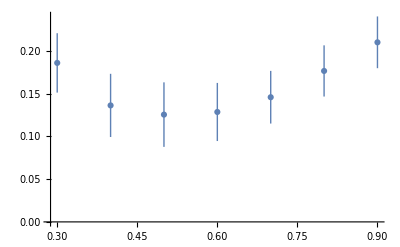
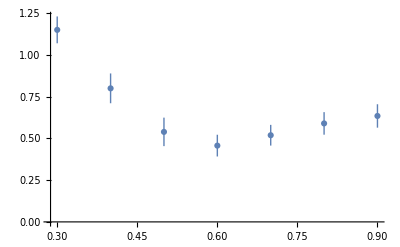
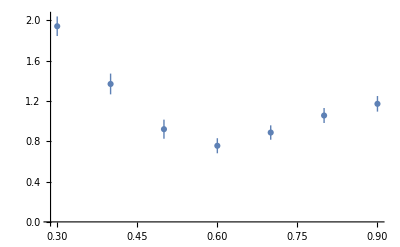
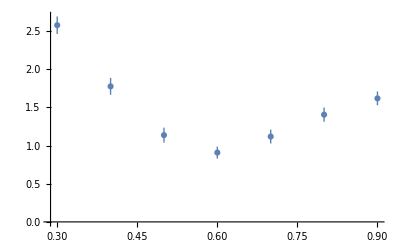
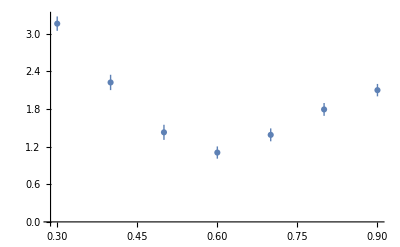
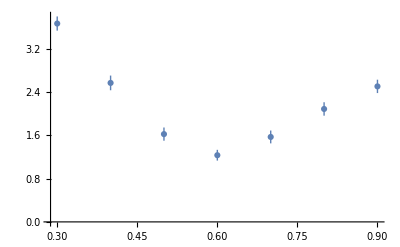
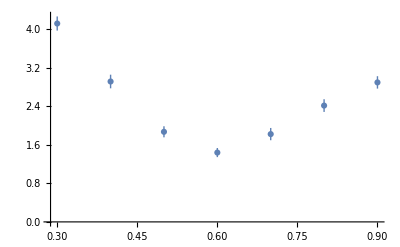
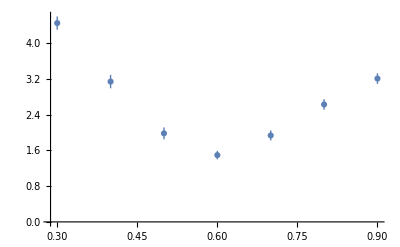
{{0.1,-Graphics-},{0.4,-Graphics-},{0.7,-Graphics-},{1.,-Graphics-},{1.3,-Graphics-},{1.6,-Graphics-},{1.9,-Graphics-},{2.2,-Graphics-},{2.5,-Graphics-},{2.8,-Graphics-},{3.1,-Graphics-},{3.4,-Graphics-},{3.7,-Graphics-}}

```mathematica
Transpose[Join[{%135},{%128}]]
```

```mathematica
Table[ListPlot[Table[{y/10+0.2,Around[Table[%125[[z]][[x]][[y]],{x,100}]]},{y,7}]],{z,13}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

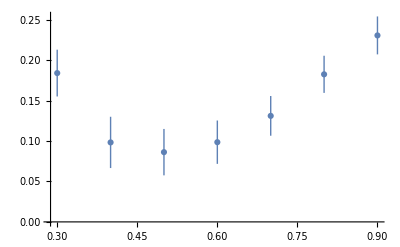
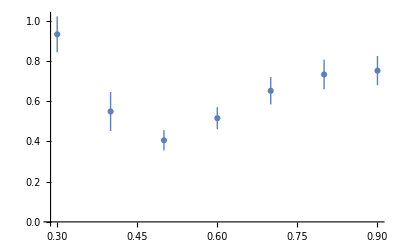
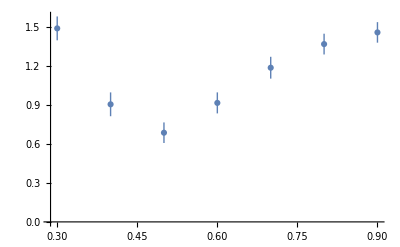
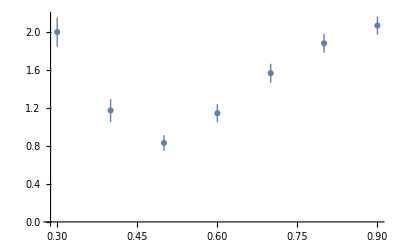
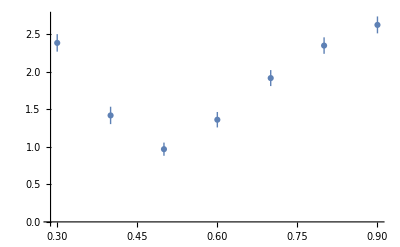
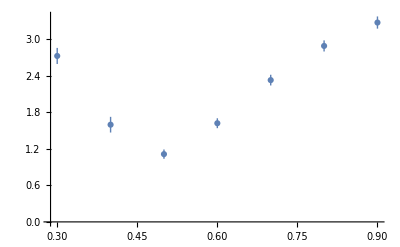
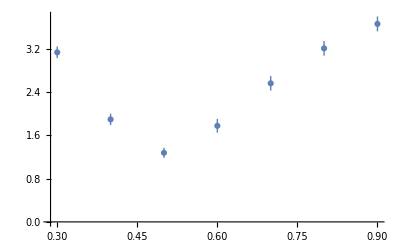
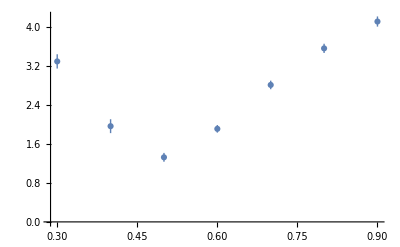

```mathematica
Table[ListPlot[Table[{y/10+0.2,Around[Table[%140[[z]][[x]][[y]],{x,20}]]},{y,7}]],{z,13}]
```

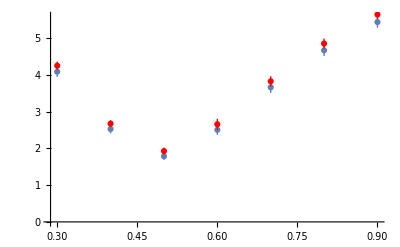

```mathematica
Show[ListPlot[Table[{y/10+0.2,Around[Table[%140[[12]][[x]][[y]],{x,20}]]},{y,7}]],ListPlot[Table[{y/10+0.2,Around[Table[%140[[13]][[x]][[y]],{x,20}]]},{y,7}],PlotStyle->Red]]
```

```mathematica
f[3]
```

{{5.23789,3.72185,2.44755,1.91115,2.40409,3.28611,4.04034},{5.50828,3.96122,2.59652,1.98122,2.41976,3.27668,4.02889},{5.08295,3.51621,2.14899,1.76381,2.45822,3.35124,4.07665},{5.15733,3.58391,2.2272,1.83456,2.44937,3.34925,4.09054},{5.44513,3.96398,2.59578,1.99732,2.46756,3.22829,3.91165},{5.13111,3.65882,2.40683,1.95954,2.49543,3.3334,4.06137},{5.36741,3.79761,2.37171,1.71308,2.20083,3.07881,3.81896},{4.98417,3.42209,2.10915,1.7134,2.34007,3.20971,3.92295},{5.54448,4.02811,2.57219,1.84283,2.20593,2.98355,3.68557},{5.49699,3.91678,2.48989,1.94621,2.46368,3.32381,4.04783},{5.45242,3.9548,2.56721,1.82895,2.31325,3.15904,3.88946},{5.27013,3.82562,2.55565,2.07926,2.57051,3.43431,4.18151},{5.30678,3.77338,2.44308,1.90263,2.35152,3.14212,3.88109},{5.2885,3.81772,2.48702,1.74622,2.08099,2.90447,3.64811},{5.42889,3.93377,2.54611,1.90492,2.39588,3.23528,3.92808},{4.97003,3.51574,2.26139,1.98104,2.68497,3.60091,4.35956},{5.15454,3.69515,2.38946,1.99007,2.61562,3.45868,4.17383},{5.20681,3.6983,2.32493,1.84238,2.31234,3.16234,3.92485},{5.33444,3.81927,2.45722,1.9613,2.49494,3.33125,4.05281},{5.16368,3.71357,2.39671,1.86788,2.47823,3.38806,4.15109},{5.24169,3.71986,2.36633,1.8003,2.32928,3.11448,3.84048},{5.12361,3.66887,2.29637,1.69759,2.24669,3.10401,3.84729},{5.45064,4.02109,2.67467,2.06816,2.5032,3.27664,3.97711},{5.31947,3.82655,2.4508,1.86053,2.38358,3.205,3.92101},{5.38224,3.77679,2.32182,1.65023,2.17223,3.00228,3.75934},{5.43492,3.90661,2.56367,1.99733,2.56314,3.40506,4.13477},{5.15755,3.63141,2.30321,1.7723,2.37346,3.28957,4.06606},{5.16102,3.66486,2.41074,1.94817,2.49068,3.3169,4.02284},{5.46959,3.85484,2.43849,1.75869,2.2028,3.06027,3.8204},{5.2291,3.61413,2.21318,1.67613,2.1976,3.12293,3.9156},{5.01769,3.48007,2.15492,1.72331,2.32358,3.22278,3.95893},{5.48928,3.98124,2.5914,1.88017,2.31403,3.13806,3.86835},{5.05509,3.51492,2.20413,1.69021,2.13843,2.96784,3.70556},{5.47104,3.98641,2.66054,2.02954,2.40221,3.27737,4.03815},{5.37155,3.84629,2.45629,1.74593,2.13605,2.96554,3.69983},{5.45132,3.93329,2.48326,1.85654,2.33649,3.22075,3.96211},{5.44817,3.86657,2.45157,1.87516,2.49816,3.39769,4.15765},{5.3569,3.75591,2.32934,1.68214,2.1764,3.05154,3.84636},{5.44951,3.94089,2.49562,1.70371,2.09633,2.92779,3.65913},{5.28678,3.81988,2.50762,1.93953,2.3973,3.22555,3.93278},{5.25668,3.69361,2.36173,1.90313,2.46323,3.29634,4.00389},{4.99539,3.51959,2.29726,1.94708,2.59493,3.41361,4.10096},{5.22887,3.74078,2.38746,1.956,2.51558,3.34643,4.08198},{5.37124,3.84712,2.5018,1.95267,2.33362,3.11912,3.85304},{5.20574,3.6637,2.36168,1.81104,2.36579,3.21749,3.98181},{5.22423,3.6459,2.32469,1.7592,2.28865,3.14579,3.87753},{5.33616,3.90523,2.57401,1.95552,2.40102,3.23157,3.95108},{5.22163,3.7606,2.4573,1.97575,2.42421,3.24788,3.98121},{5.01106,3.54904,2.2678,1.88687,2.46029,3.30968,4.04743},{5.52446,3.90764,2.4473,1.86841,2.38545,3.26061,4.00489},{5.04,3.59137,2.29024,1.75118,2.35615,3.24848,4.03251},{5.14354,3.65848,2.30757,1.79966,2.29642,3.15389,3.89793},{5.30932,3.68887,2.35808,1.73265,2.20958,3.10766,3.85497},{5.2403,3.79786,2.46474,1.90949,2.42823,3.27744,4.00213},{5.28946,3.73235,2.3805,1.76427,2.20811,3.07558,3.83766},{5.40716,3.83332,2.4098,1.79181,2.24706,3.07681,3.83605},{5.22929,3.77114,2.4905,1.92393,2.48877,3.35791,4.06154},{5.31192,3.75857,2.44309,1.81793,2.37087,3.25955,4.01751},{4.96533,3.42749,2.08212,1.726,2.40354,3.30508,4.03118},{5.29427,3.79133,2.45948,1.88514,2.45054,3.34434,4.08372},{5.10541,3.63791,2.31503,1.84062,2.47521,3.33182,4.05748},{5.1998,3.76884,2.44968,1.94949,2.44133,3.24998,3.96409},{5.24701,3.70819,2.32405,1.61021,2.03155,2.90807,3.67748},{5.28519,3.73944,2.37216,1.81115,2.30695,3.11751,3.84124},{5.44589,3.88055,2.50054,1.81955,2.29182,3.1324,3.91452},{5.52151,4.00953,2.60214,2.00827,2.46229,3.32835,4.07453},{5.15425,3.72485,2.39307,1.88836,2.43621,3.25718,3.96508},{5.32495,3.80378,2.46404,1.88034,2.34484,3.21947,4.00723},{5.29042,3.78204,2.4586,1.99125,2.53231,3.38708,4.12788},{5.21757,3.73619,2.43384,1.855,2.38941,3.22842,3.9881},{5.21025,3.63124,2.31175,1.86379,2.49293,3.3555,4.12583},{5.18065,3.63096,2.35676,1.73096,2.26857,3.13696,3.88765},{5.13803,3.64223,2.28213,1.80687,2.35249,3.18151,3.92327},{5.18147,3.68422,2.41754,1.97322,2.51498,3.32987,4.06417},{5.15226,3.61639,2.34118,1.87104,2.4976,3.35287,4.09004},{5.05216,3.45923,2.19056,1.80846,2.43298,3.28648,4.03986},{5.21599,3.66266,2.28408,1.89213,2.50701,3.4095,4.1497},{5.63288,4.11481,2.68467,1.88197,2.17453,2.97515,3.70875},{5.01603,3.41549,2.06454,1.68053,2.43537,3.42807,4.22926},{5.17852,3.59205,2.23035,1.61234,2.21638,3.12599,3.90397},{5.29024,3.7066,2.35829,1.8395,2.35178,3.22095,3.96328},{5.2954,3.73591,2.32422,1.89618,2.45954,3.28587,3.97949},{5.24318,3.6586,2.28562,1.65652,2.21761,3.12226,3.89243},{5.51545,4.0072,2.60275,1.87352,2.34455,3.14538,3.86804},{5.05245,3.46218,2.03515,1.56311,2.17589,3.06655,3.81275},{5.3531,3.85168,2.49851,1.82796,2.19239,2.95686,3.66762},{5.15331,3.64281,2.31588,1.75734,2.30034,3.12501,3.8113},{5.3298,3.80328,2.37864,1.62207,2.00161,2.85165,3.61584},{4.9672,3.46147,2.21693,2.08087,2.85101,3.77079,4.51816},{5.32388,3.8274,2.46292,1.78591,2.2253,3.05649,3.76971},{5.32271,3.82311,2.4802,1.93054,2.45433,3.31938,4.05906},{5.23123,3.68594,2.35955,1.82167,2.33739,3.2206,3.98046},{5.22012,3.73348,2.39931,1.7999,2.26604,3.15653,3.9106},{5.55654,3.95727,2.53543,1.86161,2.32402,3.19297,3.96157},{5.48221,3.88651,2.42892,1.6891,2.1356,3.03629,3.81861},{5.20771,3.68379,2.4008,2.06861,2.71631,3.56076,4.23881},{5.35368,3.80808,2.46276,1.90732,2.51765,3.34047,4.06983},{5.35915,3.77451,2.37677,1.79976,2.38186,3.2813,4.04521},{5.07614,3.58549,2.26623,1.68042,2.15925,3.06779,3.83116},{5.45325,3.97876,2.60253,1.87665,2.19687,2.97415,3.68589}}

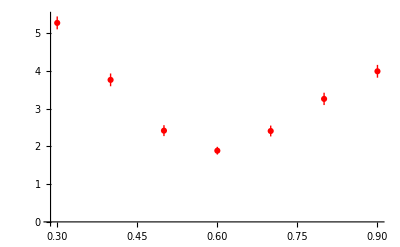

```mathematica
ListPlot[Table[{y/10+0.2,Around[Table[%18[[x]][[y]],{x,20}]]},{y,7}],PlotStyle->Red]
```